```mathematica
U(*速度*)=√((π*0.2*10*0.1/1)/2.5)
```

0.501326

```mathematica
Re=(2*0.2(*R*)*U*1(*ρ_water*))/(0.01(*粘度*))
```

Set::wrsym: 符号 Re 被保护.

89.6799

```mathematica
Co(*库郎数*)=(δt*U)/δx==1;
1*1/400/3//N
```

0.000833333

```mathematica
0.002631578947368421
```

```mathematica
ρ=1.9^2*2.5/(π*0.2*10)+1
```

2.43637

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
						(*主要的后处理程序*)
cloud=
Module[{},warcases=FindList["/Users/oc-come/Desktop/CFD/POST PROCESS/warcases.txt","case"];
		    
Quiet@Manipulate[If[i≠0,path[i_]:=StringReplace["/Users/oc-come/Desktop/CFD/cloud/Probes/casen","n"->i];
(*===========================================================*)
order=ToString[i];
(*-------------------------------------------------------------*)
			(*保存图片的路径*)
pathx=StringReplace["/Users/oc-come/Desktop/x-casei.png","i"->order];
pathxcut=StringReplace["/Users/oc-come/Desktop/xcut-casei.png","i"->order];
pathxy=StringReplace["/Users/oc-come/Desktop/xy-casei.png","i"->order];
pathspe=StringReplace["/Users/oc-come/Desktop/spe-casei.png","i"->order];(*-------------------------------------------------------------*)
data={};
data=ReadList[path@order,Number,RecordLists->True];
δt=data[[2]][[1]]-data[[1]][[1]];tfinal=data[[Length@data]][[1]];
xdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[2]]}],{j,1,Length@data}]][[2,1]];
xydata=Reap[Do[Sow[{data[[j]][[2]],data[[j]][[8]]}],{j,1,Length@data}]][[2,1]];
fig1=ListLinePlot[xdata,PlotRange->All,Ticks->Automatic,Frame->ControlActive[False,True],(*ImageSize->Large,*)PlotLabel->ControlActive[None,Text[Style[Framed["X Vs Time (case"<>order<>")"],Background->LightGreen]]],FrameLabel->ControlActive[None,{"Time","X"}],MaxPlotPoints->ControlActive[20,All]]];
(*============================================================================================*)
				(*开始做调控界面*)
Which[i==0,Import["https://www.esi-group.com/sites/default/files/company/events/5052/openfoam-logo-large.png"],
	sol=="show",fig1,
(*===========================================================================*)
			(*主要部分*)
sol=="stay",
Manipulate[
(*--------------------------------------------------------*)
fpc=Select[xdata,#[[1]]==Tcut&,1][[1]]//First;
fpc=fpc/δt;
xdatake=Reap[Do[Sow[xdata[[j]]],{j,fpc,Length@xdata}]][[2,1]];
xydatake=Reap[Do[Sow[xydata[[j]]],{j,fpc,Length@xydata}]][[2,1]];
f=Interpolation[xdatake];
fig2=Plot[f[x],{x,Tcut+1,tfinal},Ticks->Automatic,Frame->ControlActive[False,True],(*ImageSize->Large,*)FrameLabel->ControlActive[None,{"Time","X"}],PlotLabel->ControlActive[None,Text@Style[Framed["X After Tcut (case"<>order<>")"],Background->LightBlue]],PlotRange->All,PlotPoints->ControlActive[2,Automatic]];
fig4=ListLinePlot[xydatake,PlotRange->All,Frame->ControlActive[False,True],(*ImageSize->Large,*)FrameLabel->ControlActive[None,{"X","Y"}],PlotLabel->ControlActive[None,Text@Style[Framed["Space Graph(Y vs X) (case"<>order<>")"],Background->LightRed]],MaxPlotPoints->ControlActive[20,All]];
(*---------------------------------------------------------------------------------------*)
		(*求频率*)
T=Reap[Do[If[xdatake[[j]][[2]]*xdatake[[j+1]][[2]]<0,Sow[Tcut+j*δt]],{j,1,Length@xdatake}]][[2,1]];
waveLength=Reap[Do[Sow[T[[j]]-T[[j-1]]],{j,2,Length@T}]][[2,1]];
wave=2*waveLength;
calfre=1/(Mean@wave);
If[NumberQ[calfre],fre=calfre,fre="None"];
(*----------------------------------------------------------------------------------------*)
				(*傅立叶变换*)
dc=Sum[xdatake[[j]][[2]],{j,1,Length@xdatake}]/Length@xdatake;
fs=Fourier@Table[xdatake[[j]][[2]]-dc,{j,1,Length[xdatake]}];
ps=Abs[fs];
max=Max@ps;
ps=Table[{(j-1)/((δt)*Length[xdatake]),ps[[j]]},{j,1,Length[fs]}];
fsp=First@Select[ps,#[[2]]==max&,1][[1]];
fig3=ListLinePlot[ps,PlotRange->{{0,2},All},Frame->ControlActive[False,True],(*ImageSize->Large,*)FrameLabel->ControlActive[None,{"Frequency","Value"}],PlotLabel->ControlActive[None,Text@Style[Framed["Power Spectrum (case"<>order<>")"],Background->LightPink]],MaxPlotPoints->ControlActive[20,All]];
(*------------------------------------------------------------------------------------------*)
Grid[{{ControlActive[Text["Showing"],Grid[{{fig1,fig2},{fig3,fig4}},Frame->ControlActive[False,All],FrameStyle->ControlActive[None,Directive[Red,Dotted]]]]},{Grid[{{Item["Case",Background->LightGreen],i,Item["**************************",Background->Green],Item["Tcut",Background->LightBlue],Tcut},{Item["Frequency",Background->LightYellow],fre,Item["**************************",Background->Green],Item["Spectrum",Background->LightGray],fsp}},Frame->ControlActive[False,All]]}}],Style["Start Time",Bold],{{Tcut,10},δt,tfinal,InputField},Delimiter,

{print,{"No","Yes"},TrackingFunction->(If[#=="Yes",Export[pathx,fig1,ImageResolution->300];Export[pathxy,fig4,ImageResolution->300];Export[pathxcut,fig2,ImageResolution->300];Export[pathspe,fig3,ImageResolution->300]]&)},ContinuousAction->False,ControlPlacement->Top,TrackedSymbols:>Manipulate],
(*==========================================================================================*)
sol=="leave",AppendTo[warcases,"case"<>order];warcases=DeleteDuplicates@warcases;Export["/Users/oc-come/Desktop/CFD/POST PROCESS/warcases.txt",warcases]],Style["case",Bold],{{i,0},1,6,InputField},Delimiter,Style["stay or leave",Bold],{sol,{"show","stay","leave"}},ControlPlacement->Left,TrackedSymbols:>Manipulate]]

(*Export["/Users/oc-come/Desktop/CFD/MMACode/cloud.cdf",cloud]*)
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
```

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*==================================================================================*)
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*画一系列的图*)

multi=Manipulate[multifig={};Tcut=50;
Do[path[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/cloud/Freecloud/caseAn","n"->x];
data={};
order=ToString[i];
data=ReadList[path[order],Number,RecordLists->True];
δt=data[[2]][[1]]-data[[1]][[1]];xydata=Reap[Do[Sow[{data[[j]][[cxk1]],data[[j]][[cxk2]]}],{j,1,Length@data}]][[2,1]];
xydatake={};
xydatake=Reap[Do[Sow[xydata[[j]]],{j,1,Length@xydata}]][[2,1]];
fig=ListLinePlot[xydatake,PlotRange->All,Ticks->ControlActive[None,Automatic],PlotLabel->ControlActive[None,Framed["case"<>order,Background->LightGreen]],Frame->ControlActive[False,True],PlotStyle->{Yellow,Thick},FrameStyle->ControlActive[False,Directive[White]],AxesStyle->{White,Thick},Background->Black];
AppendTo[multifig,fig],
{i,begin,end}];

imcol=ImageCollage[multifig],Style[Framed["Number of Cases",Background->LightBlue],Bold],{begin,397,InputField},{end,397,InputField},Style[Framed["X-Axes",Background->LightYellow]],{{cxk1,1},{1,19,1},InputField},Style[Framed["Y-Axes"],Background->LightRed],{{cxk2,2},{1,19,1},InputField},Style[Framed["Print the Picture?",Background->LightGreen],Bold],{print,{"No","Yes"},TrackingFunction->(If[#=="Yes",Export["/Users/oc-come/Desktop/CFD/POST PROCESS/"<>ToString[cxk1]<>"-"<>ToString[cxk2]<>".jpg",imcol,ImageResolution->500]]&)},ControlPlacement->Top,TrackedSymbols:>Manipulate]
(*Export["/Users/oc-come/Desktop/CFD/MMACode/multimag.cdf",multi]*)
```

/Users/oc-come/Desktop/CFD/multimag.cdf

```mathematica
(*==========================================================================*)
(*==========================================================================*)
(*==========================================================================*)
(*==========================================================================*)
(*==========================================================================*)
```

```mathematica
(*速度的Mangnitude时间动图*)
cases=Table[i,{i,0.1,2,0.1}];figm={};
Do[cases[[10*i]]=IntegerPart[cases[[10*i]]],{i,1,Length[cases]/10}];
path[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/Template/&/U","&"->x];file[x_]:=Import[path[ToString[x]],"Data"];
cata=Map[file[#]&,cases];
cata=Map[Take[#,{23,20022}]&,cata]; 
cata=Map[StringReplace[#,{"("->"{",")"->"}"," "->","}]&,cata];
cata=Map[ToExpression@#&,cata];
len1=Length@cata[[1]];
reap[x_]:=Reap[Do[Sow[Norm[x[[i]]]],{i,1,len1}]][[2,1]];
Umcata=Map[reap[#]&,cata];
UMvsX=Map[Table[{-0.75+k*1.5/100,#[[10000+k]]},{k,1,99,1}]&,Umcata];
figm=Map[ListLinePlot@#&,UMvsX];
Export["UMvsX.gif",figm]
```

```mathematica
(*Y方向速度时间动图*)
cases=Table[i,{i,0.1,90,0.1}];figx={};
Do[cases[[10*i]]=IntegerPart[cases[[10*i]]],{i,1,Length[cases]/10}];
path[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/Template/&/U","&"->x];file[x_]:=Import[path[ToString[x]],"Data"];
cata=Map[file[#]&,cases];
cata=Map[Take[#,{23,20022}]&,cata];
cata=Map[StringReplace[#,{"("->"{",")"->"}"," "->","}]&,cata];
cata=Map[ToExpression@#&,cata];
len1=Length@cata[[1]];
reap[x_]:=Reap[Do[Sow[x[[i]][[2]]],{i,1,len1}]][[2,1]];
Uycata=Map[reap[#]&,cata];
UYvsX=Map[Table[{-0.75+k*1.5/100,#[[10000+k]]},{k,1,99,1}]&,Uycata];
figx=Map[ListLinePlot@#&,UYvsX];
Export["UYvsX.gif",figx]
```

```mathematica
(*=====================================================================*)
(*=====================================================================*)
(*=====================================================================*)
								(*画所有的图*)

Tcut=30;excel={};start=1;end=10;fig1=fig2=fig3={};
Do[path[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/Systemtic/Probes/Static/caseC_200/caseCNo./cloud.out","No."->x];
data={};
order=ToString[i];
data=ReadList[path[order],Number,RecordLists->True];
δt=data[[2]][[1]]-data[[1]][[1]];
Ttotal=First@data[[Length[data]]];
(*====================================================================*)
Fxtdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[8]]}],{j,1,Length@data}]][[2,1]];
Fxtdatake=Reap[Do[Sow[Fxtdata[[j]]],{j,(Tcut/δt)+1,Length@Fxtdata}]][[2,1]];
Fytdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[9]]}],{j,1,Length@data}]][[2,1]];
Fytdatake=Reap[Do[Sow[Fytdata[[j]]],{j,(Tcut/δt)+1,Length@Fytdata}]][[2,1]];
FxFydata=Reap[Do[Sow[{data[[j]][[8]],data[[j]][[9]]}],{j,1,Length@data}]][[2,1]];
FxFydatake=Reap[Do[Sow[FxFydata[[j]]],{j,(Tcut/δt)+1,Length@FxFydata}]][[2,1]];
(*====================================================================*)
AppendTo[fig1,ListPlot[Fxtdata,PlotRange->All]];
AppendTo[fig2,ListPlot[Fxtdatake,PlotRange->All]];
AppendTo[fig3,ListPlot[FxFytdatake,PlotRange->All]];
(*AveFx1=Sum[Fxtdata[[j]][[2]],{j,1,Length@Fxtdata}]/Length@Fxtdata;*)
(*====================================================================*)
(*AveFx=Sum[Fxtdatake[[j]][[2]],{j,1,Length@Fxtdatake}]/Length@Fxtdatake;*)
Fx={};
AppendTo[Fx,Table[Fxtdatake[[j]][[2]],{j,1,Length@Fxtdatake}]];
AveFx=Mean@Flatten@Fx;
AmpFx=(Max@Flatten@Fx-Min@Flatten@Fx)/2,
(*====================================================================*)
(*AveFx=Sum[Fxtdatake[[j]][[2]],{j,1,Length@Fxtdatake}]/Length@Fxtdatake;*)
(*Fy={};
AppendTo[Fy,Table[Fytdatake[[j]][[2]],{j,1,Length@Fytdatake}]];
AveFy=Mean@Flatten@Fy;
AmpFy=(Max@Flatten@Fy-Min@Flatten@Fy)/2;
AppendTo[excel,{"caseC"<>order,AveFx,AmpFx}],*)
{i,start,end}];
Export["/Users/oc-come/Desktop/CFD/Fx_200.xlsx",Prepend[excel,{"case","AveFx","AmpFx"}]];
```

```mathematica
(*---------------------------------------------------------------------------------------*)
(*xtdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[2]]}],{j,1,Length@data}]][[2,1]];
ytdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[3]]}],{j,1,Length@data}]][[2,1]];
xydata=Reap[Do[Sow[{data[[j]][[2]],data[[j]][[3]]}],{j,1,Length@data}]][[2,1]];
xUxdata=Reap[Do[Sow[{data[[j]][[2]],data[[j]][[5]]}],{j,1,Length@data}]][[2,1]];
Fxtdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[8]]}],{j,1,Length@data}]][[2,1]];
Ωtdata=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[16]]}],{j,1,Length@data}]][[2,1]];
xΩdata=Reap[Do[Sow[{data[[j]][[2]],data[[j]][[16]]}],{j,1,Length@data}]][[2,1]];

(*---------------------------------------------------------------------------------------*)

xydatake=Reap[Do[Sow[xydata[[j]]],{j,(Tcut/δt)+1,Length@xydata}]][[2,1]];
xtdatake=Reap[Do[Sow[xtdata[[j]]],{j,(Tcut/δt)+1,Length@xtdata}]][[2,1]];
ytdatake=Reap[Do[Sow[ytdata[[j]]],{j,(Tcut/δt)+1,Length@xtdata}]][[2,1]];
xUxdatake=Reap[Do[Sow[xUxdata[[j]]],{j,(Tcut/δt)+1,Length@xUxdata}]][[2,1]];
Fxtdatake=Reap[Do[Sow[Fxtdata[[j]]],{j,(Tcut/δt)+1,Length@Fxtdata}]][[2,1]];
Ωtdatake=Reap[Do[Sow[Ωtdata[[j]]],{j,(Tcut/δt)+1,Length@Ωtdata}]][[2,1]];
xΩdatake=Reap[Do[Sow[xΩdata[[j]]],{j,(Tcut/δt)+1,Length@Ωtdata}]][[2,1]];
(*---------------------------------------------------------------------------------------*)

(*---------------------------------------------------------------------------------------*)
						(*傅立叶变换频谱*)
fs=Fourier@Table[xtdatake[[j]][[2]],{j,1,Length[xtdatake]}];
ps=Abs[fs];
max=Max@ps;
ps=Table[{(j-1)/((δt)*Length[xtdatake]),ps[[j]]},{j,1,Length[fs]}];
fsp=First@Select[ps,#[[2]]==max&,1][[1]];

AveX=Sum[xtdatake[[j]][[2]],{j,1,Length[xtdatake]}]/Length[xtdatake];
AveY=Sum[ytdatake[[j]][[2]],{j,1,Length[ytdatake]}]/Length[ytdatake];
(*------------------------------------------------------------------------------------------------------*)
T=Reap[Do[If[xtdatake[[j]][[2]]*xtdatake[[j+1]][[2]]<0,Sow[Tcut+j*δt]],{j,1,Length@xtdatake}]][[2,1]];
waveLength=Reap[Do[Sow[T[[j]]-T[[j-1]]],{j,2,Length@T}]][[2,1]];
wave=2*waveLength;
fre=1/(Mean@wave);
(*==================================*)
yfinal=data[[Length@data]][[3]];
(*==================================*)
xdatake=Table[xtdatake[[j]][[2]],{j,1,Length@xtdatake}];
AmpX=(Max@xdatake-Min@xdatake)/2;
(*---------------------------------------------------------------------------------------------------------*)

AppendTo[excel,{"caseC"<>ToString[i],fre,fsp,AveX,AveY,AmpX,yfinal}];
(*---------------------------------------------------------------------------------------------*)
(*fig1=ListLinePlot[xtdatake,PlotRange->All,Frame->True];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/X-Tcut/case"<>order<>".jpg",fig1,ImageResolution->300];
fig11=ListLinePlot[xtdata,PlotRange->All,Frame->True];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/X-T/case"<>order<>".jpg",fig11,ImageResolution->300];*)
(*fig2=ListLinePlot[xydatake,PlotRange->All,Frame->True];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/X-Y/case"<>order<>".jpg",fig2,ImageResolution->300];
fig3=ListLinePlot[xUxdatake,PlotRange->All,Frame->True];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/X-Ux/case"<>order<>".jpg",fig3,ImageResolution->300];
fig4=ListLinePlot[Fxtdatake,PlotRange->All,Frame->True];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/Fx-T/case"<>order<>".jpg",fig4,ImageResolution->300];
fig5=ListLinePlot[Ωtdatake,PlotRange->All,Frame->True];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/W-T/case"<>order<>".jpg",fig5,ImageResolution->300];*)
(*fig6=ListLinePlot[ps,PlotRange->{{0,1},All},Frame->True];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/Spectrum/case"<>order<>".jpg",fig6,ImageResolution->300]*)
(*fig7=ListLinePlot[xΩdatake,PlotRange->{{0,1},All},Frame->True];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/W-X/case"<>order<>".jpg",fig7,ImageResolution->300]*),
(*---------------------------------------------------------------------------------------------------------*)
{i,1,10}];
Export["/Users/oc-come/Desktop/CFD/POST PROCESS/Probes/Cloud/data.xlsx",Prepend[excel,{"case","fre","fsp","AveX","AveY","AmpX","Yfinal"}]]*)
```

```mathematica
(*++++++++++++=========++++++++++++++=================+++++++++++++++++++++++=============*)
(*++++++++++++=========++++++++++++++=================+++++++++++++++++++++++=============*)
(*++++++++++++=========++++++++++++++=================+++++++++++++++++++++++=============*)
									(*探针程序*)
probes=3;startcase=25;endcase=25;
path[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/ProbeData/U/caseC_100/caseCn","n"->x];
datac={};
datac=Reap[Do[order=ToString[j];Sow[Import[path[order],"Data"]],{j,startcase,endcase}]][[2,1]];
data=Table[Take[datac[[j]],{6,Length@datac[[j]]}],{j,1,Length@datac}];
data=Table[StringReplace[data[[j]],{"("->"",")"->""}],{j,1,Length@data}];
per=Table[Flatten[Reap[Do[Sow[ImportString[data[[j]][[i]],"Table"]],{i,1,Length@data[[j]]}]][[2,1]],1],{j,1,Length@data}];
per=Map[Partition[Flatten[#,1],1+3*probes]&,per];

UXTpr=Reap[Do[Sow[Table[Table[{per[[j]][[i]][[1]],per[[j]][[i]][[2+3*m]]},{i,1,Length@per[[j]]}],{j,1,Length@per}]],{m,0,probes-1}]][[2,1]];
(*δt=UXTpr[[1]][[1]][[2]][[1]]-UXTpr[[1]][[1]][[1]][[1]];
p1=Reap[Do[Sow[Table[Table[UXTpr[[m]][[j]][[k]],{k,1,Ceiling[(100-UXTpr[[1]][[1]][[1]][[1]])/δt]}],{j,1,Length@UXTpr[[m]]}]],{m,1,Length@UXTpr}]][[2,1]];
p2=Reap[Do[Sow[Table[Table[UXTpr[[m]][[j]][[k]],{k,Ceiling[(100-UXTpr[[1]][[1]][[1]][[1]])/δt+1],Length@UXTpr[[m]][[j]]}],{j,1,Length@UXTpr[[m]]}]],{m,1,Length@UXTpr}]][[2,1]];
```

```mathematica
num=Table[i,{i,100,180,0.0005}];
Do[Do[Do[p2[[m]][[j]][[k]]=p2[[m]][[j]][[k]]/.p2[[m]][[j]][[k]][[1]]->num[[k]],{k,1,Length@p2[[m]][[j]]}],{j,1,Length@p2[[m]]}],{m,1,Length@p2}];

p2=SetPrecision[p2,7];
UXTpr=Reap[Do[Do[Sow[{Join[p1[[m]][[j]],p2[[m]][[j]]]}],{j,1,Length@p2[[m]]}],{m,1,Length@p2}]][[2,1]];*)
```

```mathematica
figXT=Reap[Do[Sow[Table[ListLinePlot[UXTpr[[m]][[j]],PlotRange->{{20,180},All}],{j,1,Length@UXTpr[[m]]}]],{m,1,Length@UXTpr}]][[2,1]];
figXT[[3]][[1]]
```

-Graphics-

```mathematica
Do[order=ToString[i];Export["/USers/oc-come/Desktop/CFD/POST PROCESS/Probes/Use/Xt/caseC"<>order<>".png",figXT[[1]][[i-24]],ImageResolution->300],{i,startcase,endcase}]
```

```mathematica
Tcut=0;δt=UXTpr[[1]][[1]][[2]][[1]]-UXTpr[[1]][[1]][[1]][[1]];
Tnum=Floor[Tcut/δt(*+(Tcut-60.0003)/0.0003*)]
Tfinal=180;
Tfin=Floor[Tfinal/δt]
```

40000

120000

```mathematica
UX=Reap[Do[Sow[Table[Table[UXTpr[[m]][[j]][[i]][[2]],{i,Tnum,(*Length@UXTpr[[m]][[j]]*)Tfin}],{j,1,Length@UXTpr[[m]]}]],{m,1,Length@UXTpr}]][[2,1]];UXsum=Reap[Do[Sow[Table[Mean[UX[[m]][[i]]],{i,1,Length@UX[[m]]}]],{m,1,Length@UX}]][[2,1]];
UX0=Reap[Do[Sow[Table[UX[[m]][[i]]-UXsum[[m]][[i]],{i,1,Length@UX[[m]]}]],{m,1,Length@UX}]][[2,1]];
fs=Reap[Do[Sow[Table[Fourier@UX0[[m]][[i]],{i,1,Length@UX0[[m]]}]],{m,1,Length@UX0}]][[2,1]];
ps=Abs@fs;
max=Reap[Do[Sow[Table[Max@ps[[m]][[j]],{j,1,Length@ps[[m]]}]],{m,1,Length@ps}]][[2,1]];
psv=Reap[Do[Sow[Table[Table[{(i-1)/((δt)*Length@UX0[[m]][[j]]),ps[[m]][[j]][[i]]},{i,1,Length@ps[[m]][[j]]}],{j,1,Length@UX0[[m]]}]],{m,1,Length@ps}]][[2,1]];
```

```mathematica
figX=Reap[Do[Sow[Table[ListLinePlot[psv[[m]][[j]],PlotRange->{{0,5},All}],{j,1,Length@psv[[m]]}]],{m,1,Length@psv}]][[2,1]];
fspX=Reap[Do[Sow[Table[First@Select[psv[[m]][[j]],#[[2]]==max[[m]][[j]]&,1][[1]],{j,1,Length@psv[[m]]}]],{m,1,Length@psv}]][[2,1]];
```

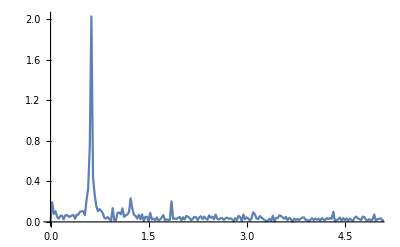
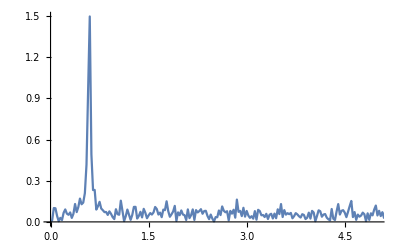
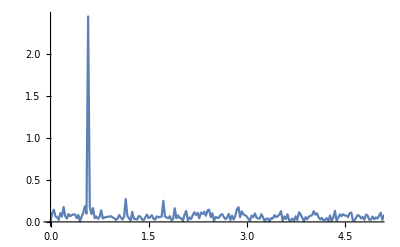
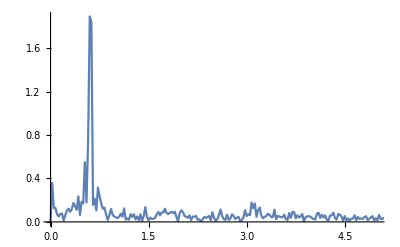
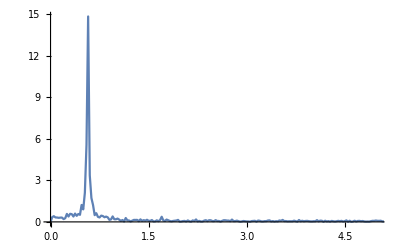
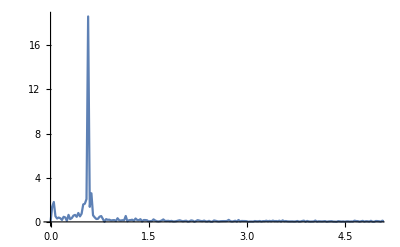
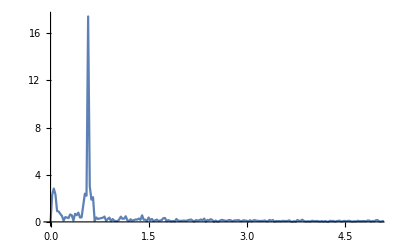
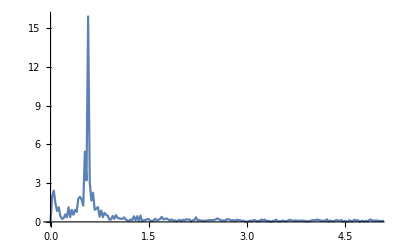

```mathematica
figX[[1]]
```

```mathematica
Do[order=ToString[i];Export["/USers/oc-come/Desktop/CFD/POST PROCESS/Probes/Use/Spe/caseC"<>order<>".png",figX[[1]][[i-16]],ImageResolution->300],{i,startcase,endcase}]
```

```mathematica
fspX[[1]]
```

{0.624992,0.599993,0.574993,0.599993,0.574993,0.574993,0.574993,0.574993}

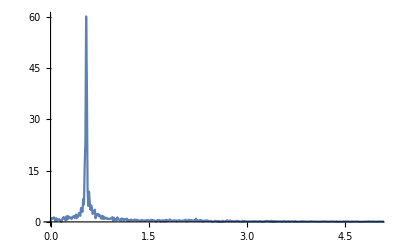

{0.544441}

```mathematica
caseC26figX=figX[[1]]
caseC26fspX=fspX[[1]]
```

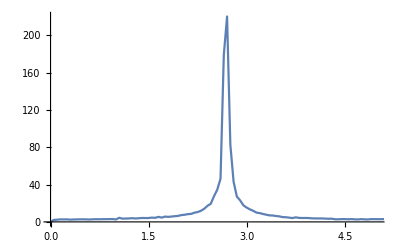
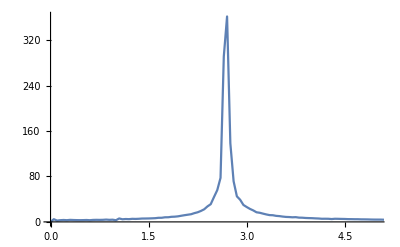
{{-Graphics-},{-Graphics-},{-Graphics-}}

{{2.69991},{2.69991},{2.69991}}

```mathematica
caseC28figX=figX
caseC28fspX=fspX
```

```mathematica
UYTpr=Reap[Do[Sow[Table[Table[{per[[j]][[i]][[1]],per[[j]][[i]][[3+3*m]]},{i,1,Length@per[[j]]}],{j,1,Length@per}]],{m,0,probes-1}]][[2,1]];
figYT=Reap[Do[Sow[Table[ListLinePlot[UYTpr[[m]][[j]],PlotRange->All],{j,1,Length@UYTpr[[m]]}]],{m,1,Length@UYTpr}]][[2,1]];
```

```mathematica
Tcut=10;δt=UYTpr[[1]][[1]][[2]][[1]]-UYTpr[[1]][[1]][[1]][[1]];
Tnum=Tcut/δt;
UY=Reap[Do[Sow[Table[Table[UYTpr[[m]][[j]][[i]][[2]],{i,Tnum,Length@UYTpr[[m]][[j]]}],{j,1,Length@UYTpr[[m]]}]],{m,1,Length@UYTpr}]][[2,1]];UYsum=Reap[Do[Sow[Table[Mean[UY[[m]][[i]]],{i,1,Length@UY[[m]]}]],{m,1,Length@UY}]][[2,1]];
UY0=Reap[Do[Sow[Table[UY[[m]][[i]]-UYsum[[m]][[i]],{i,1,Length@UY[[m]]}]],{m,1,Length@UY}]][[2,1]];
fs=Reap[Do[Sow[Table[Fourier@UY0[[m]][[i]],{i,1,Length@UY0[[m]]}]],{m,1,Length@UY0}]][[2,1]];
ps=Abs@fs;
max=Reap[Do[Sow[Table[Max@ps[[m]][[j]],{j,1,Length@ps[[m]]}]],{m,1,Length@ps}]][[2,1]];
psv=Reap[Do[Sow[Table[Table[{(i-1)/((δt)*Length@UY0[[m]][[j]]),ps[[m]][[j]][[i]]},{i,1,Length@ps[[m]][[j]]}],{j,1,Length@UY0[[m]]}]],{m,1,Length@ps}]][[2,1]];
figY=Reap[Do[Sow[Table[ListLinePlot[psv[[m]][[j]],PlotRange->{{0,5},All}],{j,1,Length@psv[[m]]}]],{m,1,Length@psv}]][[2,1]];
fspY=Reap[Do[Sow[Table[First@Select[psv[[m]][[j]],#[[2]]==max[[m]][[j]]&,1][[1]],{j,1,Length@psv[[m]]}]],{m,1,Length@psv}]][[2,1]];
```

```mathematica
endcase=10;probes=15;startcase=6;
path[x_]:=StringReplace["/Users/oc-come/Desktop/CFD/ProbeData/P/caseB/caseBn","n"->x];
datac={};
datac=Reap[Do[order=ToString[j];Sow[Import[path[order],"Data"]],{j,startcase,endcase}]][[2,1]];
data=Table[Take[datac[[j]],{18,Length@datac[[j]]}],{j,1,Length@datac}];
(*data=Table[StringReplace[data[[j]],{"("->"",")"->""}],{j,1,Length@data}];*)
per=Table[Flatten[Reap[Do[Sow[ImportString[data[[j]][[i]],"Table"]],{i,1,Length@data[[j]]}]][[2,1]],1],{j,1,Length@data}];
```

```mathematica
PTpr=Reap[Do[Sow[Table[Table[{per[[i]][[j]][[1]],per[[i]][[j]][[2+m]]},{j,1,Length[per[[i]]]}],{i,1,Length@per}]],{m,0,probes-1}]][[2,1]];
```

```mathematica
figP=Reap[Do[Sow[Table[ListLinePlot[PTpr[[m]][[j]],PlotRange->{{5,30},{-10,10}}],{j,1,Length@PTpr[[m]]}]],{m,1,Length@PTpr}]][[2,1]][[1]]
```

```mathematica
(*=++++++++++============+++++++++++++++==========++++++++++++++++==========-------——————————————*)
(*=++++++++++============+++++++++++++++==========++++++++++++++++==========-------——————————————*)
(*=++++++++++============+++++++++++++++==========++++++++++++++++==========-------——————————————*)
                                                                                     (*探针线程序*)
time="10";fig={};ckc={};ps1="caseC_100";ps2="caseC_200";ps=ps1;r=0.2;Yc=0.3;
f[x_,y_,ps_]:=StringReplace["/Users/oc-come/Desktop/CFD/Systemtic/Probes/Static/choose/caseCNO./postProcessing/singleGraph/time/line_U.xy",{"NO."->x,"time"->y,"choose"->ps}];
Do[order=ToString[i];
data=Import[f[order,time,ps],"Table"];
UYT=Reap[Do[Sow[{data[[j]][[1]],data[[j]][[3]]}],{j,1,Length@data}]][[2,1]];
Y=Interpolation[UYT];
t1=(*y/.First@FindRoot[Y[y],{y,0.5}]*)r+Yc;
t2=y/.First@FindRoot[Y[y],{y,1,2}];
Which[t1≠t2&&Abs[t2-t1]>0.7,lenY=Text@Style[Abs[t2-t1],Green],t1==t2||Abs[t2-t1]≤0.7,lenY=Text@Style["not satisfied in 2",Red]];
AppendTo[ckc,lenY];
AppendTo[fig,ListLinePlot[UYT,PlotRange->All,PlotLegends->Placed[{Framed[Text@Style["case"<>order<>"'s length is "ckc[[i]],White],FrameStyle->Orange,Background->Black]},Above]]],
{i,1,10}];

Which[ps=="caseC_100",ck1=ckc,ps=="caseC_200",ck2=ckc,ps=="caseC_400",ck3=ckc];
```

InterpolatingFunction::dmval: 输入值 {-7.84203} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {-4.44166} 位于插值函数的数据范围之外. 将使用外推法.

```mathematica
Row[Framed/@{Column[Table[Text["case"<>ToString[i]],{i,1,10}]],Column[ck1],Column[ck2],Column[ck3]}]
```

case1
case2
case3
case4
case5
case6
case7
case8
case9
case10not satisfied in 2
not satisfied in 2
1.38978
1.36772
1.35879
1.35451
1.3511
1.34816
1.34481
1.34181not satisfied in 2
not satisfied in 2
1.38084
1.35986
1.35237
1.34883
1.34638
1.34426
1.34194
1.33954Column[ck3]

1
 |  |  |  |